## Parameters and data importation

```mathematica
(*Here, I define most of the parameters that will be used throughout the model:

beginDate is the ordinal date at which the model begins (273) which corresponds to 1 October.

totalDays is the total number of days this model will run through,beginning with 1 October,2013 and ending with 31 August,2014.

minChillTemp and maxChillTemp are the minimum and maximum temperatures at which plants accumulate chilling units (CUs).
r 
chillRequirement is the minimum number of CUs a plant must accumulate in order to undergo vernalization.
tBasePlant and tBaseInsect are the base temperatures used in calculating growing degree days (GDDs).

targetGDDPlant and target GDDInsect are the number of growing degree days for plants and insects to flower or emerge, respectively.

replications is the total number of replications, which includes temperature increases from 0 (startDT) to endDT degrees C, in 0.1 degree increments. replications is calculated so that endDT is the only variable that needs to be changed when deciding to run the program with a different range of temperatures.*)

beginDate=273;
totalDays=334;
minChillTemp=0;
maxChillTemp=7.2;
chillRequirement=300;
tBasePlant=7;
tBaseInsect=9;
targetGDDPlant=230;
targetGDDInsect=90;
startDT=0;
endDT=5;
replications=endDT*10+1;


(*I'm importing data file from NOAA, featuring climate data in Benton County Oregon in 2013 and 2014. The data file includes various irrelevant data, but it is left unaltered so that datasets in the same format can be used for different locations.*)

dataRaw=Import["/Users/natalia/BentonClimate.csv"];

(*These four arrays are created to store chill, flowering, and emergence dates, mismatch, and deltaT. There will be one data value for each replication (for each 0.1 degrees).
The rest of the arrays used in the program will be created right before they are filled, in their respective sections. The four arrays below are those that will be used to plot the results.*)

chillingDates=ConstantArray[c,replications];
floweringDates=ConstantArray[c,replications];
emergenceDates=ConstantArray[c,replications];
mismatchArray=ConstantArray[c,replications];
allTemperatures=ConstantArray[c,replications];
(*allTemperatures stores values from startDT to endDT, incremented by 0.1 degree C.*)
```

## Data isolation

```mathematica
(*I'm creating a two-dimensional array to store ordinal date, daily minimum temperature, and daily maximum temperature. The array will include 334 days from 1 October, 2013 through 31 August, 2014.*)
dataFormatted=ConstantArray[c,{3,totalDays}];

(*This function converts yyyymmdd format dates into ordinal dates. It is necessary to make the imported data usable.

First, the year is isolated by multiplying and rounding (20130101 -> 2013.0101 -> 2013).
Then this value is multiplied times 10000 and subtracted from the data (20130101 - 2013 = 0101), leaving the month and day.
The day is calcualted by subtracting 10000*year and 100*month from data (20130101 - 2013 - 0100 = 01), leaving the day.
Several If statements determine the number of days to add to the day value, depending on the month.*)
ordinalDateFunction[date_]:=
(
year=Floor[date/10000];
month=Floor[(date-10000*year)/100];
day=date-10000*year-100*month;

If[month==01,ordinalDate=day];
If[month==02,ordinalDate=day+31];
If[month==03,ordinalDate=day+59];
If[month==04,ordinalDate=day+90];
If[month==05,ordinalDate=day+120];
If[month==06,ordinalDate=day+151];
If[month==07,ordinalDate=day+181];
If[month==08,ordinalDate=day+212];
If[month==09,ordinalDate=day+243];
If[month==10,ordinalDate=day+273];
If[month==11,ordinalDate=day+304];
If[month==12,ordinalDate=day+334];

Return[ordinalDate];
)


(*This  loop fills the dataFormatted array with values from the csv file. Degrees are in tenths of a degree C in the data file, so they are converted to whole degrees C as they're put into the array. 
Dates are in a yyyymmdd format, so they're converted into ordinal dates via ordinalDateFunction as they're stored in the array.*)
For[n=1,n≤totalDays,n++,{
(*date*)
dataFormatted[[1,n]]=ordinalDateFunction[dataRaw[[(274+n),6]]];
(*daily min temperature (tMin)*)
dataFormatted[[2,n]]=(dataRaw[[(274+n),12]]/10);
(*daily max temperature (tMax)*)
dataFormatted[[3,n]]=(dataRaw[[(274+n),7]]/10);
}];
```

## Temperature Interpolation

```mathematica
(*This multiline function uses the ordinal date to calculate solarDeclination.*)
solarDeclinationFunction[ordinalDate_]:=
(
gamma=(2Pi/365)*(ordinalDate-1);

solarDeclination=0.006918-0.3999Cos[gamma]+0.070257Sin[gamma]-0.006758Cos[2gamma]+0.000907Sin[2gamma]-0.002697Cos[3gamma]+0.00148Sin[3gamma];

Return[solarDeclination];
)


(*This multiline function claculates dayLength using latitude and ordinal date.*)
dayLengthFunction[latitude_,ordinalDate_]:=
(
latitudeRadians=latitude*Pi/180;

dayLength=(180/Pi)*((2/15)*ArcCos[-Tan[latitudeRadians]*Tan[solarDeclinationFunction[ordinalDate]]]);

Return[dayLength];
)


(*This function is written like a multiline function for consistency and legibility. It uses tMin and tMax, the number of hours since sunrise (hourFromRise), latitude, and the ordinal date to calculate a temperature for each daylight hour.*)
hourDayTempFunction[tMin_,tMax_,hourFromRise_,latitude_,ordinalDate_]:=
(
hourDayTemp=tMin+(tMax-tMin)*Sin[(Pi*hourFromRise)/(dayLengthFunction[latitude,ordinalDate]+4)];

Return[hourDayTemp];
)


(*I found the sunset temperature by calling the hourDayTempFunction, using the dayLengthFunction as an argument. hourNightTempFunction calculates a temperature for each nighttime hour using tMin, tMax, the number of hours since sunset (hourFromSet), latitude, and the ordinal date.*)
hourNightTempFunction[tMin_,tMax_,hourFromSet_,latitude_,ordinalDate_]:=
(
hourNightTemp=hourDayTempFunction[tMin,tMax,dayLengthFunction[latitude,ordinalDate],latitude,ordinalDate]-Log[hourFromSet]*((hourDayTempFunction[tMin,tMax,dayLengthFunction[latitude,ordinalDate],latitude,ordinalDate]-tMin)/Log[24-dayLengthFunction[latitude,ordinalDate]]);

Return[hourNightTemp];
)


(*hourTempFunction uses tMin, tMax, the number of hours from 0000 (hour), latitude, and the ordinal date and returns the temperature for any hour in a given day. I've then used If statements to determine whether hourTempFunction should call the hourDayTempFunction or the hourNightTempFunction. It was necessary to consider hours between sunrise and sunset inclusive to be daylight hours, because of the way the hourNightTempFunction and the hourDayTempFunction interact.*)
hourTempFunction[tMin_,tMax_,hour_,latitude_,ordinalDate_]:=
(
sunriseTime=12-dayLength/2;
sunsetTime=12+dayLength/2;

If[(sunsetTime+1)> hour≥sunriseTime,{hourFromRise=hour-sunriseTime;hourTemp=hourDayTempFunction[tMin,tMax,hourFromRise,latitude,ordinalDate]}];

If[hour<sunriseTime,{hourFromSet=(24-sunsetTime)+hour;hourTemp=hourNightTempFunction[tMin,tMax,hourFromSet,latitude,ordinalDate]}];

If[hour≥ (sunsetTime+1),{hourFromSet=hour-sunsetTime;hourTemp=hourNightTempFunction[tMin,tMax,hourFromSet,latitude,ordinalDate]}];

Return[hourTemp];
)


(*This function must be run before the hourTempFunction will work.*)
hourDayTempFunction[0,20,5,44,120];



(*A two-dimensional array is created for hourly temperature data for the 334 dates. There are 8016 total hours (24 hours per 334 days).*)
temperatureData=ConstantArray[c,{5,(totalDays*24)}];


(*This loop fills temperatureData with day, hour, and temperature using hourTempFunction. There are 24 hours in the day, beginning with 0 and ending with 23.*)
n=1;
For[day=1,day≤totalDays,day++,{
For[hour=0,hour≤23,hour++,{
(*day*)
temperatureData[[1,n]]=dataFormatted[[1,day]];
(*hour*)
temperatureData[[2,n]]=hour;
(*hourly temperature*)
temperatureData[[3,n]]=hourTempFunction[dataFormatted[[2,day]],dataFormatted[[3,day]],hour,dataRaw[[2,4]],dataFormatted[[1,day]]];
n++;
}]
}]
```

## Chilling Units

```mathematica
(*This function calculates the number of chilling units acquired in a given hour, using the hourly temperature, as stored in temperatureData, and minChillTemp and maxChillTemp.*)
chillingUnitsFunction[hourlyTemp_,minChillTemp_,maxChillTemp_]:=
(

If[hourlyTemp≤minChillTemp,chillUnit=0];
If[minChillTemp<hourlyTemp≤maxChillTemp,chillUnit=1];
If[hourlyTemp>maxChillTemp,chillUnit=0];

Return[chillUnit];
)


(*This function contains a loop that runs through each hour in temperatureData and uses chillingUnitsFunction to calculate CUs, storing them in the fourth element of the same array. deltaT is added to each temperature value to allow for multiple replications.*)
FillChill[deltaT_]:=For[b=1,b≤(totalDays*24),b++,{

temperatureData[[4,b]]=chillingUnitsFunction[temperatureData[[3,b]]+deltaT,minChillTemp,maxChillTemp];

}]


(*This loop uses the FillChill function and a nested For loop to calculate the date at which enough CUs have accumulated, running replications times with temperatures from startDT to endDT. It compiles cumulative CUs until the chillRequirement has been reached, and then records the date. sumChill is initially defined and set equal to zero, because the number of CUs already accumulated before beginDate is zero.

The allTemperatures array is filled with each temperature so that they can be used as x values when the final data is plotted.

A counter variable is used to stand for the number of times through the loop, and allows me to point to the right date in the chillingDates array, as well as the right value in the allTemperatures array.*)

counter=0;

For[n=startDT,n≤endDT,n=(n+(endDT-startDT)/(replications-1)),{

FillChill[n];

sumChill=0;

counter++;

For[r=1,sumChill<chillRequirement,r++,{

sumChill=sumChill+temperatureData[[4,r]];

chillDate=temperatureData[[1,r]];

chillingDates[[counter]]=chillDate;

}];

allTemperatures[[counter]]=n;

}]
```

## Growing Degrees

```mathematica
(*These functions calculate the number of GDDs the plant or insect has accumulated in any given day, using the base temperatures and tMin and tMax.*)
growingDegreePlantFunction[tBasePlant_,tMin_,tMax_]:=gddPlant=((tMax+tMin)/2)-tBasePlant

growingDegreeInsectFunction[tBaseInsect_,tMin_,tMax_]:=gddInsect=((tMax+tMin)/2)-tBaseInsect


(*I'm creating an array to store daily plant GDDs and insect GDDs. This array will be used for temporary data storage when running through a for loop in the next section.*)
growingDegreeData=ConstantArray[c,{2,totalDays}];


(*This function contains a loop that calculates GDDs for both plants and insects, and stores these values in the growingDegreeData array. tMin and tMax values are used from the dataFormatted array. The If statements convert negative GDD values to zero, so that GDDs cannot be lost.
deltaT is added to each temperature value so that multiple replications can be carried out.*)
FillGDD[deltaT_]:=For[n=1,n≤totalDays,n++,{
growingDegreeData[[1,n]]=growingDegreePlantFunction[tBasePlant,dataFormatted[[2,n]]+deltaT,dataFormatted[[3,n]]+deltaT];
If[growingDegreeData[[1,n]]<0,growingDegreeData[[1,n]]=0];

growingDegreeData[[2,n]]=growingDegreeInsectFunction[tBaseInsect,dataFormatted[[2,n]]+deltaT,dataFormatted[[3,n]]+deltaT];
If[growingDegreeData[[2,n]]<0,growingDegreeData[[2,n]]=0];
}]
```

## Flowering and emergence dates and mismatch

```mathematica
(*This loop uses the FillGDD function to calculate GDD accumulation over replications (variable) replications, using temperatures startDT through endDT. Flowering and emergence take place when the plant or insect has accumulated sufficient GDDs. The loop stops when the sum GDDs reach the target GDD requirement, and dates are foudn by referring to the first element of the dataFormattedArray. The loop then stores flowering dates and emergence dates in floweringDates and emergenceDates for each replication.
sumGDDP and sumGDDI are defined and set to zero at the beginning of each trip through the loop.

startGDDPlant is defined so that plants don't begin accumulating GDDs until vernalization has occurred (until the chill date has passed). Chill dates from the chillingDates array are converted into startGDDPlant dates, so that they refer to the corresponding number in the array instead of existing as ordinal dates.

Insects begin accumulating GDDs on ordinal date 1, which is converted into startGDDInsect. startGDDInsect refers to the number in the array, rather than the ordinal date.*)

counter=0;

For[d=startDT,d≤endDT,d=(d+(endDT-startDT)/(replications-1)),{

FillGDD[d];

counter++;
sumGDDP=0;
sumGDDI=0;

startGDDPlant=chillingDates[[counter]]-beginDate;

If[chillingDates[[counter]]<beginDate,startGDDPlant=(365+chillingDates[[counter]])-beginDate];

For[k=startGDDPlant,sumGDDP<targetGDDPlant,k++,{

sumGDDP=sumGDDP+growingDegreeData[[1,k]];
floweringDate=dataFormatted[[1,k]];
floweringDates[[counter]]=floweringDate;

}];


startGDDInsect=(365+1)-beginDate;

For[g=startGDDInsect,sumGDDI<targetGDDInsect,g++,{

sumGDDI=sumGDDI+growingDegreeData[[2,g]];
emergenceDate=dataFormatted[[1,g]];
emergenceDates[[counter]]=emergenceDate;

}]
}]
```

## Results: Flowering and emergence dates and mismatch

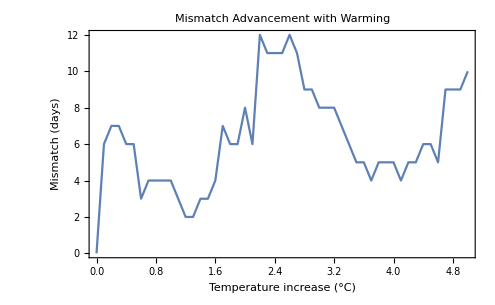

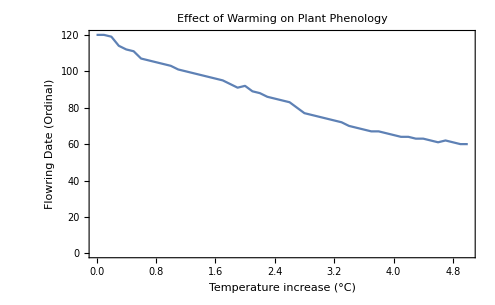

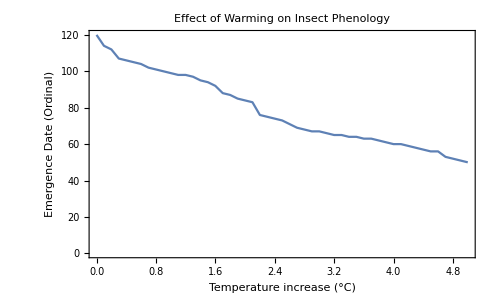

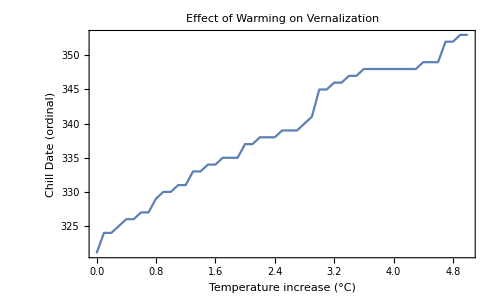

```mathematica
(*Finally, mismatch is calculated by subtracting the flowering date from the emergence date in the following for loop. Mismatch values are stored in mismatchArray.*)

For[n=1,n≤replications,n++,{
mismatchArray[[n]]=floweringDates[[n]]-emergenceDates[[n]];
}]


(*Here, I'm creating four sets of data, featuring deltaT as the x variable and mismatch values, flowering dates, emergence dates, and chill dates as y variables.*)
mismatchData=Transpose[{allTemperatures,mismatchArray}];
floweringData=Transpose[{allTemperatures,floweringDates}];
emergenceData=Transpose[{allTemperatures,emergenceDates}];
chillData=Transpose[{allTemperatures,chillingDates}];


(*Finally, I'm creating four plots that show how mismatch, flowering date, insect emergence, and chill date are affected by temperature increases.*)
ListPlot[mismatchData,PlotLabel->"Mismatch Advancement with Warming",LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Joined->True,Frame->True,BaseStyle->17,FrameLabel->{"Temperature increase (°C)","Mismatch (days)"}]

ListPlot[floweringData,PlotLabel->"Effect of Warming on Plant Phenology",LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Joined->True,Frame->True,BaseStyle->17,FrameLabel->{"Temperature increase (°C)","Flowring Date (Ordinal)"}]

ListPlot[emergenceData,PlotLabel->"Effect of Warming on Insect Phenology",LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Joined->True,Frame->True,BaseStyle->17,FrameLabel->{"Temperature increase (°C)","Emergence Date (Ordinal)"}]

ListPlot[chillData,PlotLabel->"Effect of Warming on Vernalization",LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Joined->True,Frame->True,BaseStyle->17,FrameLabel->{"Temperature increase (°C)","Chill Date (ordinal)"}]
```